## 1.Feladat

{InterpolatingFunction[…],InterpolatingFunction[…]}

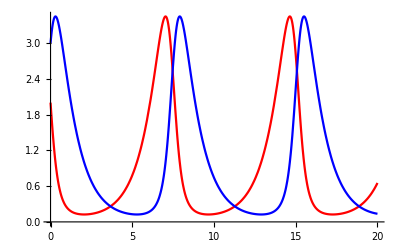

```mathematica
{xsol,ysol}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==2,y[0]==3},{x,y},{t,0,20}]

Plot[{xsol[t],ysol[t]},{t,0,20}, PlotStyle->{Red, Blue}]
```

```mathematica
ParametricPlot3D[{t,xsol[t],ysol[t]},{t,0,20}, PlotStyle->{Blue}]
```

-Graphics3D-

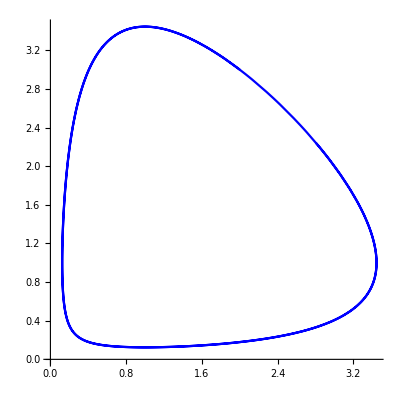

```mathematica
ParametricPlot[{xsol[t],ysol[t]},{t,0,15}, PlotStyle->Blue]
```

## 2.Feladat

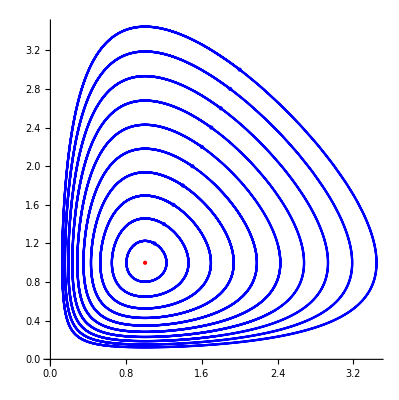

```mathematica
xs=Table[2-i/10,{i,0,9}];
ys=Table[3-2*i/10,{i,0,9}];

{xsol1,ysol1}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,1],y[0]==Part[ys,1]},{x,y},{t,0,20}];

{xsol2,ysol2}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,2],y[0]==Part[ys,2]},{x,y},{t,0,20}];

{xsol3,ysol3}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,3],y[0]==Part[ys,3]},{x,y},{t,0,20}];


{xsol4,ysol4}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,4],y[0]==Part[ys,4]},{x,y},{t,0,20}];


{xsol5,ysol5}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,5],y[0]==Part[ys,5]},{x,y},{t,0,20}];


{xsol6,ysol6}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,6],y[0]==Part[ys,6]},{x,y},{t,0,20}];


{xsol7,ysol7}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,7],y[0]==Part[ys,7]},{x,y},{t,0,20}];


{xsol8,ysol8}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,8],y[0]==Part[ys,8]},{x,y},{t,0,20}];

{xsol9,ysol9}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,9],y[0]==Part[ys,9]},{x,y},{t,0,20}];

{xsol10,ysol10}=NDSolveValue[{x'[t]==x[t]-x[t]*y[t],y'[t]==- y[t]+x[t]*y[t],x[0]==Part[xs,10],y[0]==Part[ys,10]},{x,y},{t,0,20}];


Show[ParametricPlot[{{xsol1[t],ysol1[t]},
{xsol2[t],ysol2[t]},
{xsol3[t],ysol3[t]},
{xsol4[t],ysol4[t]},
{xsol5[t],ysol5[t]},
{xsol6[t],ysol6[t]},
{xsol7[t],ysol7[t]},
{xsol8[t],ysol8[t]},
{xsol9[t],ysol9[t]},
{xsol10[t],ysol10[t]}},{t,0,20}, PlotStyle->Blue
],
Graphics[{PointSize[Large],Blue,Point[Table[{Part[xs,i],Part[ys,i]},{i,1,10}]]}],
Graphics[{PointSize[Large],Red,Point[{1,1}]}]
]
```

## 3.Feladat

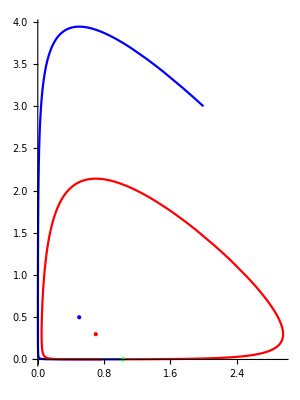

```mathematica
epsz=0.2;
a=0.5;
b=1;
c=0.5;
d=1;

{xsol,ysol}=NDSolveValue[{x'[t]==a*x[t]-b*x[t]*y[t],y'[t]==-c* y[t]+d*x[t]*y[t],x[0]==2,y[0]==3},{x,y},{t,0,20}];

{xsol2,ysol2}=NDSolveValue[{x'[t]==(a-epsz)*x[t]-b*x[t]*y[t],y'[t]==- (c+epsz)*y[t]+d*x[t]*y[t],x[20]==xsol[20],y[20]==ysol[20]},{x,y},{t,20,40}];

Show[
ParametricPlot[{xsol[t],ysol[t]},{t,0,20}, PlotStyle->Blue],
ParametricPlot[{xsol2[t],ysol2[t]},{t,20,40}, PlotStyle->Red],
Graphics[{PointSize[Large],Blue,Point[{c/d,a/b}]}],
Graphics[{PointSize[Large],Red,Point[{(c+epsz)/d,(a-epsz)/b}]}],Graphics[{PointSize[Large],Green,Point[{xsol[20],ysol[20]}]}],
PlotRange-> All
]
```

## 4.Feladat

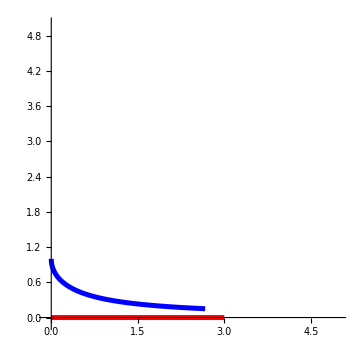

```mathematica
vg=1;
vk=2;
{xsol,ysol}=NDSolveValue[{
x'[t]==vg*(vk*t-x[t])/Sqrt[(vk*t-x[t])^2+y[t]^2],
y'[t]==(-vg)* y[t]/Sqrt[(vk*t-x[t])^2+y[t]^2],
x[0]==0,y[0]==1},
{x,y},{t,0,3}];
Show[
ParametricPlot[{xsol[t],ysol[t]},{t,0,3}, PlotStyle->{Thickness[0.01],Blue},PlotRange->{{-0.1,5},{-0.1,5}}],
ParametricPlot[{t,0},{t,0,3}, PlotStyle->{Thickness[0.01],Red}]
]
```

## 5.Feladat

```mathematica
va=1;
vb=1;
vc=1;

{{xas,yas},{xbs,ybs},{xcs,ycs}}=NDSolveValue[{
xa'[t]==va*(xb[t]-xa[t])/Sqrt[(xb[t]-xa[t])^2+(yb[t]-ya[t])^2],ya'[t]==va*(yb[t]-ya[t])/Sqrt[(xb[t]-xa[t])^2+(yb[t]-ya[t])^2],xb'[t]==vb*(xc[t]-xb[t])/Sqrt[(xc[t]-xb[t])^2+(yc[t]-yb[t])^2],yb'[t]==vb*(yc[t]-yb[t])/Sqrt[(xc[t]-xb[t])^2+(yc[t]-yb[t])^2],xc'[t]==vc*(xa[t]-xc[t])/Sqrt[(xa[t]-xc[t])^2+(ya[t]-yc[t])^2],yc'[t]==vc*(ya[t]-yc[t])/Sqrt[(xa[t]-xc[t])^2+(ya[t]-yc[t])^2],
xa[0]==5,ya[0]==0,
xb[0]==-5/2,yb[0]==5*Sqrt[3]/2,
xc[0]==-5/2,yc[0]==-5*Sqrt[3]/2},
{{xa,ya},{xb,yb},{xc,yc}},{t,0,5.77}];
Show[
ParametricPlot[{{xas[t],yas[t]},{xbs[t],ybs[t]},{xcs[t],ycs[t]}},{t,0,5.77}, PlotStyle->{{Brown,Thickness[0.008]},{Purple,Thickness[0.008]},{Orange,Thickness[0.008]}},PlotRange->{{-5.5,5.5},{-5.5,5.5}}]
]
```

NDSolveValue::mxst: Maximum number of 177795 steps reached at the point t == 5.05523.

-Graphics-